# E4: Introduction to Capacitors and the RC Circuit

## Priyanka Makin Maya Fabrikant 10/27/2016

## Introduction

In this lab we learned about capacitors and their capacitance and we experimented with assembling resistor-capacitor (RC) circuits. We first explored the effects of plate area and distance on the capacitance of a capacitor. We learned that all capacitors have a stray capacitance that needs to be taken into account. Then we constructed a more complex circuit with a resistor, capacitor, and a switch so we could analyze the exponential decy of the voltage across the capacitor when the switch is opened.

## Part 1: Capacitance of Parallel Plates

Distance^-1 in m^-1 | Capacitance in F
618.429 | 5.563×10^-9
309.215 | 2.803×10^-9
206.143 | 1.903×10^-9
154.607 | 1.483×10^-9
123.686 | 1.203×10^-9
103.072 | 1.033×10^-9

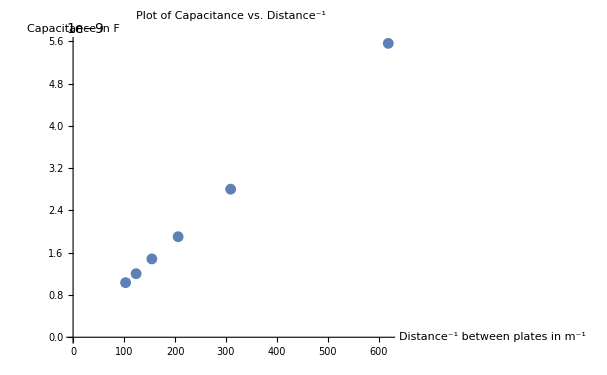

```mathematica
Aplate = 0.09456; (*Plate Area in m^2*)
Cstray = 1.7*10^-11; (*Stray Capacitance in F*)
T = 0.001617; (*Average Thickness of a Nylon Washer in m*)

W = {1, 2, 3, 4, 5, 6}; (*Number of Washers*)
C1 = {0.558, 0.282, 0.192, 0.150, 0.122, 0.105} * 10^-8; (*Inter-Plate Capacitance in F*)

d = T*W; (*Calculating the actual distance between plate in m*)
C2 = C1 - Cstray; (*Calculatinf the actual Capacitance in F*)

Cvsinvd = Thread[{1/d, C2}]; (*Making the data*)

Grid[Prepend[Cvsinvd, {"Distance^-1 in m^-1", "Capacitance in F"}], Frame->All] (*Cute Tables*)

ListPlot[Cvsinvd, PlotLabel->"Plot of Capacitance vs. Distance^-1",AxesLabel->{"Distance^-1 between plates in m^-1", "Capacitance in F"}] (*Cute Graph*)
```

From the data in the graph and the chart, we can see that as the invers of the distance between the plates increase the capacitance also increases. The trend seems to at least look relatively linear. And this agrees with the known equation C = ϵ_0A/d. If we look at the inverse of distance capacitance can be expressed by C = ϵ_0 Ad^-1.

```mathematica
eps0 = (C2*d)/Aplate;
eps0avg = (∑_(i=1)^Length[eps0] eps0[[i]])/Length[eps0]
eps0sd = √((∑_(i=1)^Length[eps0] (eps0[[i]] - eps0avg)^2)/(Length[eps0] - 1));
eps0sdom = eps0sd/√Length[eps0]
```

9.9817×10^-11

1.75462×10^-12

Our measured value of ϵ_0 = (9.98 ± 0.02) * 10^-11. However ϵ_0 is a constant and was given to us in the lab write up as ϵ_0 = 8.85*10^-12 F/m. Do they agree? Well, the actual value of ϵ_0 minus our measured value is 8.85 - 9.98 = 1.13 which is greater than three times the uncertainty, 3 * 0.02 = 0.06. Therefore, our measured value of ϵ_0 does not agree with the actual value.

## Part 2: Measurement of the Time Constant of an RC Circuit

```mathematica
time = {0, 1.2, 2.9, 5, 7.8, 11.3, 16.3, 25.7, 28.2, 30.6, 36, 41} * 10^-3; (*Decay Time in s*)
voltage = {3.48, 3.08, 2.68, 2.28, 1.88, 1.48, 1.08, 0.6, 0.48, 0.40, 0.32, 0.20}; (*Decay in Voltage in V*)
lnvoltage = Log[voltage];
lnvvst = Thread[{time, lnvoltage}]
```

{{0,1.24703},{0.0012,1.12493},{0.0029,0.985817},{1/200,0.824175},{0.0078,0.631272},{0.0113,0.392042},{0.0163,0.076961},{0.0257,-0.510826},{0.0282,-0.733969},{0.0306,-0.916291},{9/250,-1.13943},{41/1000,-1.60944}}

```mathematica
(*Use this data for the best fit line*)
time2 = {0, 1.2, 2.9, 5, 7.8, 11.3, 16.3};
voltage2 = {3.48, 3.08, 2.68, 2.28, 1.88, 1.48, 1.08};
lnvoltage2 = Log[voltage2];

x = time2;
y = lnvoltage2;
L  = Length[x];

Δ=L*∑_(i=1)^L (x[[i]])^2-(∑_(i=1)^L x[[i]])^2
```

1443.24

```mathematica
m=1/Δ(L*∑_(i=1)^L (x[[i]]*y[[i]])-(∑_(i=1)^L x[[i]])*∑_(i=1)^L y[[i]]) (*Slope*)
```

-67.3279

```mathematica
b=1/Δ((∑_(i=1)^L (x[[i]])^2*∑_(i=1)^L y[[i]])-(∑_(i=1)^L x[[i]])*(∑_(i=1)^L (x[[i]]*y[[i]]))) (*Y-Intercept*)
```

1.18682

```mathematica
σy=√(1/(L-2)*∑_(i=1)^L (y[[i]]-(m*x[[i]]+b))^2)
```

0.045956

```mathematica
δm=√((L*σy^2)/Δ) (*Error in Slope*)
```

0.953733

```mathematica
δb=√((σy^2*∑_(i=1)^L (x[[i]])^2)/Δ) (*Error in Y-Intercept*)
```

0.0210725

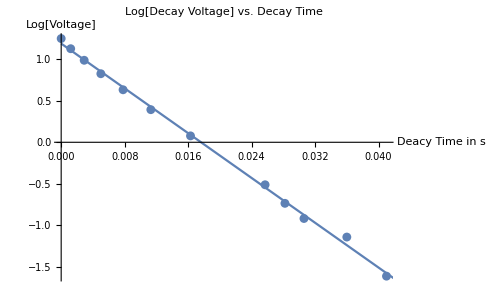

```mathematica
DataPlot = ListPlot[lnvvst];
TheoryPlot = Plot[m*q+b, {q, 0, 0.05}];
Show[DataPlot, TheoryPlot, PlotLabel ->"Log[Decay Voltage] vs. Decay Time", AxesLabel -> {"Deacy Time in s", "Log[Voltage]"}]
```

The data in our graph looks pretty good, the relationship between time and the log(voltage) seems to be relatively linear. If we were to just relate voltage to time we would get an exponential decay graph. Our data dips below the x-axis because the log of a voltage less than 1V is a negative number.

```mathematica
tau = -1/m
δtau = Abs[δm/m^2] (*Can you derive this from the Master Ruler?*)
```

0.0148527

0.000210396

Hence, the measured time constant, τ, using linear regression is (1.50 ± 0.02) * 10^-2s. When we calculate the RC constant directly, we get R * C = 518 * (1.838 * 10^-5) = 0.00952 s. If we compare these values we can determine if they agree or not. The actual measurement minus our calculated measurement is 0.00952 - 0.0150 = 0.0055 which is greater than the uncertainty multiplied by 3, 0.0002 * 3 = 0.0006, so the measured value disagrees with our calculated value.

## Conclusion

In conclusion, this was a vital lab in helping us understand the functionality of capacitors and the behavior of RC circuits. Looking back on the lab execution and our collected data, I guess we weren’t as accurate as we could have been. For both our measured value of ϵ_0 and measured value of τ, we got that they didn’t agree with the calculated values. We could have come across some errors in reading the capacitance meter correctly or the parallel plate capacitor could have had some excess charge on it that changed our collected data. Overall, many things could have caused error in our data but I still think that our data still says enough about the relationship between the various things we measured (capacitance and plate distance, voltage and decay time in an RC circuit).